## Scientific Programming 5

Manipulating polynomials

### A cyclotomic polynomial

```mathematica
Factor[z^15-1]
```

(-1+z) (1+z+z^2) (1+z+z^2+z^3+z^4) (1-z+z^3-z^4+z^5-z^7+z^8)

```mathematica
Φ[z_]:=1-z+z^3-z^4+z^5-z^7+z^8
```

```mathematica
G={1,2,4,7,8,11,13,14};
```

```mathematica
?PolynomialRemainder
```

PolynomialRemainder[p,q,x] gives the remainder from dividing p by q, treated as polynomials in x.

```mathematica
PolynomialRemainder[Φ[z^2],Φ[z],z]
```

0

```mathematica
PolynomialReduce[Φ[z^2],Φ[z],z]
```

{{1+z-z^3-z^4-z^5+z^7+z^8},0}

```mathematica
Table[PolynomialRemainder[Φ[z^g],Φ[z],z],{g,G}]
```

{0,0,0,0,0,0,0,0}

```mathematica
Solve[Φ[w]==0]
```

{{w→-(-1)^(1/15)},{w→(-1)^(2/15)},{w→(-1)^(4/15)},{w→-(-1)^(7/15)},{w→(-1)^(8/15)},{w→-(-1)^(11/15)},{w→-(-1)^(13/15)},{w→(-1)^(14/15)}}

```mathematica
Solve[Φ[w]==0]/. {(-1)^(1/15)->-z, (-1)^(j_/15)->(-1)^j z^j}
```

{{w→z},{w→(-1)^(2/15)},{w→(-1)^(4/15)},{w→-(-1)^(7/15)},{w→(-1)^(8/15)},{w→-(-1)^(11/15)},{w→-(-1)^(13/15)},{w→(-1)^(14/15)}}

```mathematica
(-1)^(2/15)//FullForm
```

Power[-1,Rational[2,15]]

```mathematica
Solve[Φ[w]==0]/. {(-1)^(1/15)->-z, Power[-1,Rational[j_,15]]->(-1)^j z^j}
```

{{w→z},{w→z^2},{w→z^4},{w→z^7},{w→z^8},{w→z^11},{w→z^13},{w→z^14}}

### Groebner basis

Compute a Groebner basis

```mathematica
gb=GroebnerBasis[{x^2-2 y^2,x y-3},{x,y}]
```

{-9+2 y^4,3 x-2 y^3}

```mathematica
Solve[gb==0]
```

{{x→-2^(1/4) √3,y→-(√3)/2^(1/4)},{x→ⅈ 2^(1/4) √3,y→-(ⅈ √3)/2^(1/4)},{x→-ⅈ 2^(1/4) √3,y→(ⅈ √3)/2^(1/4)},{x→2^(1/4) √3,y→(√3)/2^(1/4)}}

```mathematica
Solve[{x^2-2 y^2,x y-3}==0]
```

{{x→-2^(1/4) √3,y→-(√3)/2^(1/4)},{x→-ⅈ 2^(1/4) √3,y→(ⅈ √3)/2^(1/4)},{x→ⅈ 2^(1/4) √3,y→-(ⅈ √3)/2^(1/4)},{x→2^(1/4) √3,y→(√3)/2^(1/4)}}

Prove that polynomials have no common roots:

```mathematica
GroebnerBasis[{x+y,x^2-1,y^2-2x},{x,y}]
```

{1}

```mathematica
NSolve[{x+y,x^2-1,y^2-2x}==0]
```

{}

```mathematica
polys={3 x^2+y z-5x-1, 2x+3 x y+y^2,x-3y+x z-2 z^2};
```

```mathematica
GroebnerBasis[polys,{x,y,z}]
```

{-1772-710 z+3653 z^2+748 z^3+711 z^4+3064 z^5-314 z^6-896 z^7+72 z^8,2919537727088+42907663790334 y+3928775021139 z+28114074864208 z^2-54650967173 z^3+1797838568888 z^4-1818218283354 z^5-940700863552 z^6+85799291400 z^7,101977837394420+85815327580668 x-44563746052776 z-132499058173595 z^2+96518479090729 z^3-119620552893922 z^4-37331258048706 z^5+46653549404648 z^6-3431808123192 z^7}

```mathematica
gb7=GroebnerBasis[polys,{x,y,z},Modulus->7]
```

{6+6 z+z^2+4 z^3+3 z^4+6 z^5+3 z^6+z^7,1+4 y+4 z+y z+4 z^3+z^4+z^6,1+3 y+y^2+6 z^2+3 z^3+3 z^4+3 z^5+4 z^6,1+x+y+3 z+2 z^2+2 z^3+6 z^4+z^5}

### Working with algebraic extensions

```mathematica
Clear[z]
```

```mathematica
M={{-1,5 z^3,5 z^2,-5z,-5 z^4,1},
  {4 z^2,5(z+z^4),5(z+z^2),0,0,z^2},
  {4 z^3,5(z^3+z^4),5(z+z^4),0,0,z^3},
  {-6 z^4,0,0,-5(z^2+z^3),-5(z^2+z^4),z^4},
  {-6z,0,0,-5(z+z^3),-5(z^2+z^3),z},
  {24,30 z^3,30 z^2,20z,20 z^4,1}};
```

```mathematica
M//MatrixForm
```

(-1 | 5 z^3 | 5 z^2 | -5 z | -5 z^4 | 1
4 z^2 | 5 (z+z^4) | 5 (z+z^2) | 0 | 0 | z^2
4 z^3 | 5 (z^3+z^4) | 5 (z+z^4) | 0 | 0 | z^3
-6 z^4 | 0 | 0 | -5 (z^2+z^3) | -5 (z^2+z^4) | z^4
-6 z | 0 | 0 | -5 (z+z^3) | -5 (z^2+z^3) | z
24 | 30 z^3 | 30 z^2 | 20 z | 20 z^4 | 1)

```mathematica
p=Collect[
CharacteristicPolynomial[M,λ],λ,Simplify]
```

15625 (-1+z)^5 z^5 (-1-2 z+z^2+15 z^3+50 z^4+93 z^5+122 z^6+114 z^7+70 z^8+30 z^9+8 z^10)+6250 z^4 (-2+2 z+2 z^2+5 z^3+5 z^4-15 z^5-4 z^6-19 z^7+20 z^8+20 z^9-9 z^10+2 z^11-8 z^12+z^15) λ-625 (-1+z)^2 z^2 (1-3 z-9 z^2-10 z^3-10 z^4+3 z^6+4 z^7+15 z^8+20 z^9+9 z^10+5 z^11) λ^2+250 (-1+z)^2 z (1+z+3 z^3+6 z^4+15 z^5+15 z^6+6 z^7+3 z^8) λ^3+25 (-1+z^2-5 z^3-4 z^4-8 z^5-4 z^6-5 z^7+z^8) λ^4-10 (-1+z)^2 z (1+z) λ^5+λ^6

```mathematica
cpoly=
Collect[
CharacteristicPolynomial[M,λ],λ,Simplify[PolynomialRemainder[#,1+z+z^2+z^3+z^4,z]]&]
```

1953125+156250 (1+2 z^2+2 z^3) λ-15625 λ^2-2500 (1+2 z^2+2 z^3) λ^3-125 λ^4+10 (1+2 z^2+2 z^3) λ^5+λ^6

```mathematica
(1+2 z^2+2 z^3)/.z->ⅇ^(2π ⅈ/5)//FullSimplify
```

-√5

```mathematica
(1+2 z^2+2 z^3)/.z->ⅇ^(4π ⅈ/5) //FullSimplify
```

√5

```mathematica
cpoly1=Collect[cpoly/.z->ⅇ^(2π ⅈ/5),λ,FullSimplify]
```

1953125-156250 √5 λ-15625 λ^2+2500 √5 λ^3-125 λ^4-10 √5 λ^5+λ^6

```mathematica
Factor[cpoly1,Extension->√5]
```

(5 √5-λ)^4 (5 √5+λ)^2

```mathematica
cpoly2=Collect[cpoly/.z->ⅇ^(4π ⅈ/5),λ,FullSimplify]
```

1953125+156250 √5 λ-15625 λ^2-2500 √5 λ^3-125 λ^4+10 √5 λ^5+λ^6

Notice that √5 has changed sign

```mathematica
Factor[cpoly2,Extension->√5]
```

(5 √5-λ)^2 (5 √5+λ)^4

So the characteristic polynomial looks as if it is

```mathematica
p=(λ+5(1+2 z^2+2 z^3))^4 (λ-5(1+2 z^2+2 z^3))^2;
```

```mathematica
Collect[p,λ,Simplify[PolynomialRemainder[#,1+z+z^2+z^3+z^4,z]]&]
```

1953125+156250 (1+2 z^2+2 z^3) λ-15625 λ^2-2500 (1+2 z^2+2 z^3) λ^3-125 λ^4+10 (1+2 z^2+2 z^3) λ^5+λ^6

```mathematica
%-cpoly
```

0

A first look at graphics

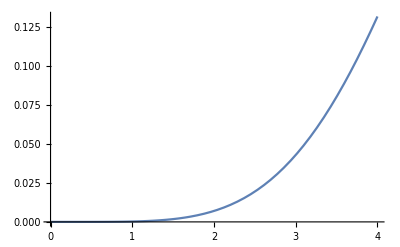

```mathematica
Plot[BesselJ[5,x],{x,0,4}]
```

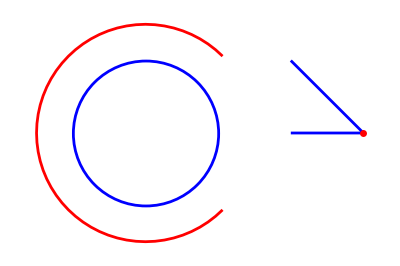

```mathematica
Graphics[{
Blue,AbsoluteThickness[2],Line[{{0,0},{1,0},{0,1}}],
Red,AbsolutePointSize[5],Point[{1,0}],
Blue,Circle[{-2,0},1],Red,Circle[{-2,0},1.5,{π/4,7π/4}]}
                   ]
```

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semi-axes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

```mathematica
?EdgeForm
```

EdgeForm[g] is a graphics directive which specifies that edges of polygons and other filled graphics objects are to be drawn using the graphics directive or list of directives g.

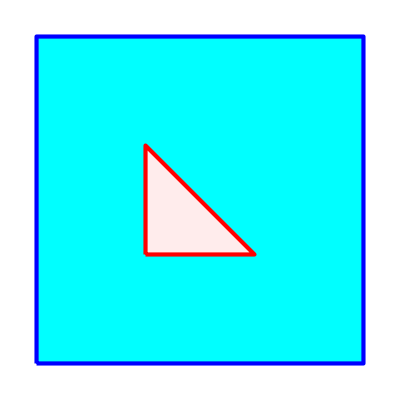

```mathematica
Graphics[{
{Cyan,EdgeForm[{AbsoluteThickness[3],RGBColor[0,0,1]}],Rectangle[{-1,-1},{2,2}]},
{EdgeForm[{AbsoluteThickness[3],RGBColor[1,0,0]}],FaceForm[LightPink],Polygon[{{0,0},{1,0},{0,1}}]} }
                   ]
```

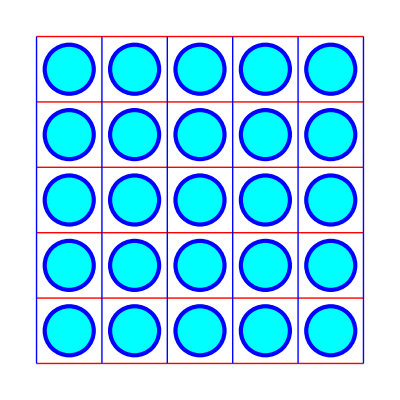

```mathematica
Graphics[{
Red,Table[Line[{{0,y},{1,y}}], {y,0,1,0.2}],
Blue,Table[Line[{{x,0},{x,1}}], {x,0,1,0.2}],
 Cyan, EdgeForm[{AbsoluteThickness[3],RGBColor[0,0,1]}],Table[Disk[{x,y},0.075],{x,0.1,0.9,0.2},{y,0.1,0.9,0.2}]}
                 ]
```

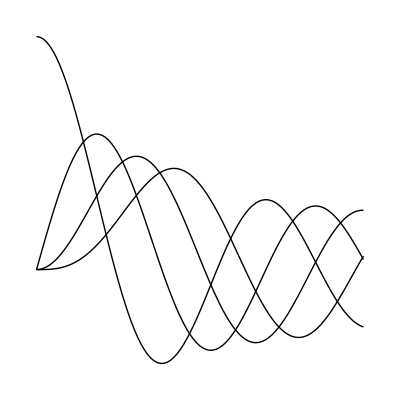

```mathematica
Graphics[{
Line[ Table[{x, BesselJ[n,x]},{n,0,3},{x,0,10,0.1}] ]},
  AspectRatio->1
                  ]
```

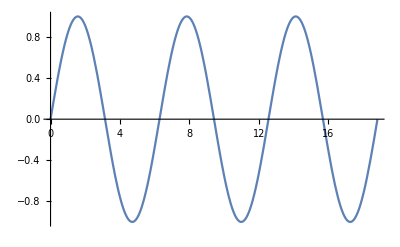

```mathematica
Plot[Sin[x],{x,0,6Pi},
         ImageSize->400]
```

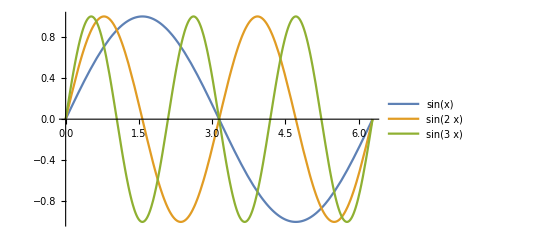

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},
          PlotLegends->"Expressions",
          ImageSize->400]
```

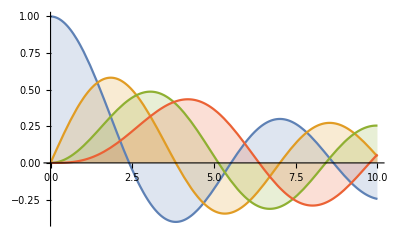

```mathematica
g1=
Plot[Evaluate[Table[BesselJ[n,x],{n,0,3}]],{x,0,10},
         Filling->Axis,
        ImageSize->400]
```

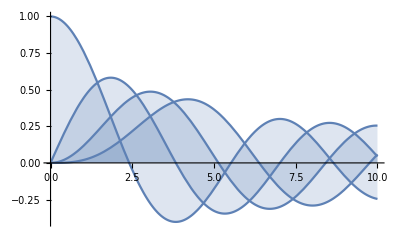

```mathematica
g2=Plot[Table[BesselJ[n,x],{n,0,3}],{x,0,10},
         Filling->Axis,
        ImageSize->400]
```

```mathematica
f[n_,x_]:= Abs[((1/Pi)^(1/4)HermiteH[n,x])/(E^(x^2/2)Sqrt[2^n n!])]^2
```

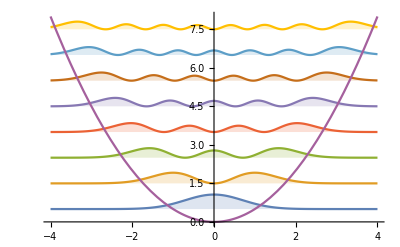

```mathematica
Plot[Evaluate@
  Append[Table[f[n,x]+n+1/2,{n,0,7}],x^2/2],{x,-4,4},Filling-> Table[n->n-1/2,{n,1,8}],
ImageSize->400]
```

```mathematica
Clear[f]
```

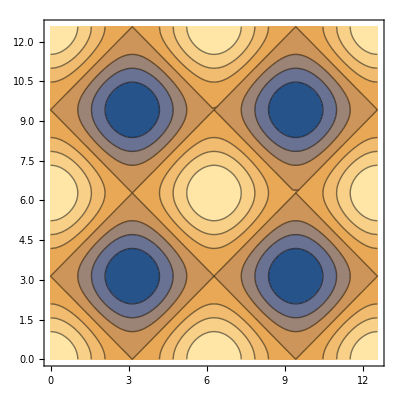

```mathematica
g3=ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi},
                         ImageSize->400]
```

```mathematica
Options[ContourPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

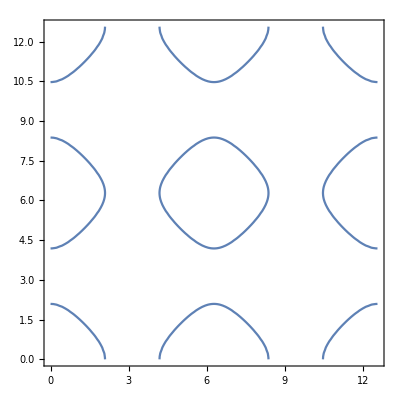

```mathematica
g4=ContourPlot[Cos[x]+Cos[y]==1/2,{x,0,4Pi},{y,0,4Pi}]
```

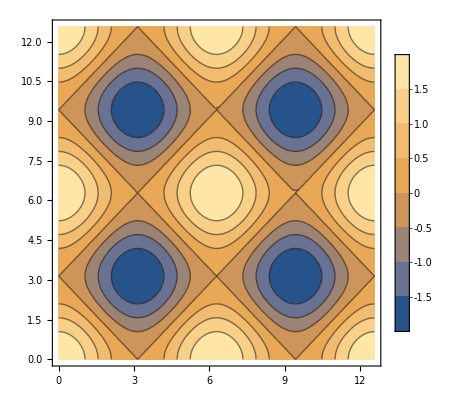

```mathematica
ContourPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi},PlotLegends->Automatic]
```

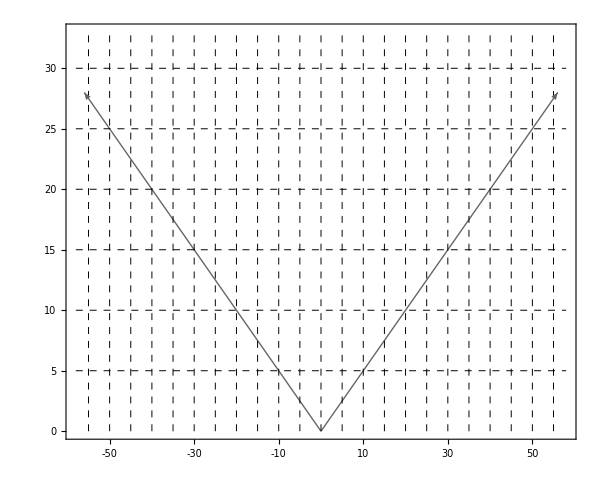

```mathematica
Graphics[{AbsoluteThickness[1],GrayLevel[0.4],Arrowheads[0.03],
Arrow[{{0,0},{56,28}}],Arrow[{{0,0},{-56,28}}],
{Dashed,Black,AbsoluteThickness[0.7],
Table[Line[{{k,0},{k,33}}],{k,-55,55,5}],
Table[Line[{{-58,k},{58,k}}],{k,5,30,5}]},
GrayLevel[0.2]},
AspectRatio->0.8,
PlotRange->{{-58,58},{0,33}},
Frame->True,
FrameTicks->{{Table[Which[Mod[n,10]==0,{n,n,{0.02,0}},
                                                 Mod[n,5]==0,{n,n,{0.015,0}},
                                                True,{n,Null,{0.01,0}}],{n,0,33}],
                         Table[Which[Mod[n,10]==0,{n,Null,{0.02,0}},
                                               Mod[n,5]==0,{n,Null,{0.015,0}},
                                               True,{n,Null,{0.01,0}}],{n,0,33}]},
                         {Table[Which[Mod[n,10]==0,{n,If[n≥0,n ,n Spacer[10]],{0.02,0}},
                                                Mod[n,5]==0,{n,Null,{0.015,0}},
                                               True,{n,Null,{0.01,0}}],{n,-58,58}],
                          Table[Which[Mod[n,10]==0,{n,Null,{0.02,0}},
                                                Mod[n,5]==0,{n,Null,{0.015,0}},
                                                True,{n,Null,{0.01,0}}],{n,-58,58}]} },
FrameStyle->Directive[{FontFamily->"Times", FontSize->17}],
ImageSize->600]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},
             ColorFunction->"Rainbow",
              ImageSize->400,
               BoxRatios->{1,1,1}
                ]
```

-Graphics3D-

```mathematica
?ViewPoint
```

ViewPoint is an option for Graphics3D and related functions which gives the point in space from which three-dimensional objects are to be viewed.

```mathematica
?Opacity
```

RowBox[{"Opacity", "[", StyleBox["a", "TI"], "]"}] is a graphics directive which specifies that graphical objects which follow are to be displayed, if possible, with opacity StyleBox["a", "TI"]. 
RowBox[{"Opacity", "[", RowBox[{StyleBox["a", "TI"], ",", StyleBox["color", "TI"]}], "]"}] uses the specified color with opacity StyleBox["a", "TI"].

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},
             PlotStyle-> Opacity[0.5] ]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(3+Cos[v])Cos[u],(3+Cos[v])Sin[u],Sin[v]},{u,0,2Pi},{v,0,2Pi},
   ImageSize->400,
       Ticks->False]
```

-Graphics3D-

```mathematica
?ColorData
```

ColorData[scheme] gives a function that generates colors in the named color scheme when applied to parameter values. 
ColorData[scheme,property] gives the specified property of a color scheme.
ColorData[collection] gives a list of color schemes in a named collection.
ColorData[] gives a list of named collections of color schemes.

```mathematica
?ColorFunction
```

ColorFunction is an option for graphics functions that specifies a function to apply to determine colors of elements.

```mathematica
g1
```

-Graphics-

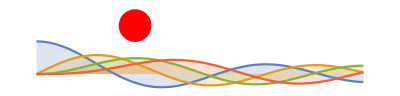

```mathematica
Show[{g1,
Graphics[{Red,Disk[{3,1.5},0.5]}]},
Axes->False,
PlotRange->All,
AspectRatio->Automatic]
```

```mathematica
?GraphicsGrid
```

GraphicsGrid[{{g_11,g_12,…},…}] generates a graphic in which the g_ij are laid out in a two-dimensional grid.

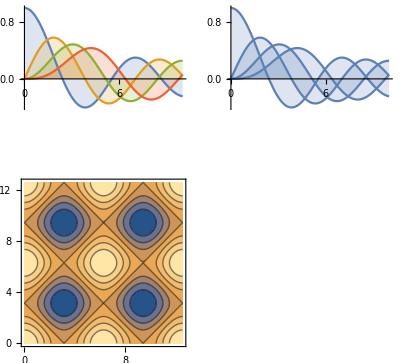

```mathematica
GraphicsGrid[{{g1,g2},{g3,g4}},
ImageSize->400]
```